```mathematica
Clear[sin,cos]
r={{cos,sin},{-sin,cos}}
sig={{sigx,tauxy},{tauxy,sigy}}
sigr=Transpose[r].sig.r//FullSimplify
```

{{cos,sin},{-sin,cos}}

{{sigx,tauxy},{tauxy,sigy}}

{{cos^2 sigx+sigy sin^2-2 cos sin tauxy,cos (sigx-sigy) sin+cos^2 tauxy-sin^2 tauxy},{cos (sigx sin+cos tauxy)-sin (cos sigy+sin tauxy),cos^2 sigy+sigx sin^2+2 cos sin tauxy}}

```mathematica
ArcSin[0.8]180/Pi
```

53.1301

{{0,0},{cos,sin}}

{{cos,sin},{cos-sin,cos+sin}}

{{cos-sin,cos+sin},{-sin,cos}}

{{-sin,cos},{0,0}}

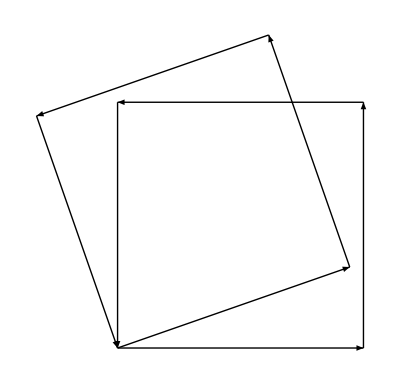

```mathematica
pt1={0,0};
pt2={1,0};
pt3={1,1};
pt4={0,1};
v1=pt2-pt1;
v2=pt3-pt2;
v3=pt4-pt3;
v4=pt4-pt1;
Clear[sin,cos]
v1r={pt1,pt2}.r
v2r={pt2,pt3}.r
v3r={pt3,pt4}.r
v4r={pt4,pt1}.r
angle=ArcTan[20. Degree];
sin=Sin[angle];
cos=Cos[angle];
Graphics[{Arrow[{pt1,pt2}],Arrow[{pt2,pt3}],Arrow[{pt3,pt4}],Arrow[{pt4,pt1}],Arrow[v1r],Arrow[v2r],Arrow[v3r],Arrow[v4r]}]
```

```mathematica
Clear[sin,cos,t]

subst={cos->Cos[t],sin->Sin[t]}
subst2={Cos[t]->cos,Sin[t]->sin}
sr=sigr[[1,1]]/.subst
tr=sigr[[1,2]]/.subst
dtr=D[tr,t]
```

{cos→Cos[t],sin→Sin[t]}

{Cos[t]→cos,Sin[t]→sin}

sigx Cos[t]^2-2 tauxy Cos[t] Sin[t]+sigy Sin[t]^2

tauxy Cos[t]^2+(sigx-sigy) Cos[t] Sin[t]-tauxy Sin[t]^2

(sigx-sigy) Cos[t]^2-4 tauxy Cos[t] Sin[t]-(sigx-sigy) Sin[t]^2

```mathematica
sr
```

sigx Cos[t]^2-2 tauxy Cos[t] Sin[t]+sigy Sin[t]^2

```mathematica
sigr[[1,1]]
```

cos^2 sigx+sigy sin^2-2 cos sin tauxy

```mathematica
(*AntiHorario*)
Clear[sin,cos]
r={{cos,-sin},{sin,cos}};
sig={{sigx,tauxy},{tauxy,sigy}};
sigr=Transpose[r].sig.r//FullSimplify;
sigr[[1,1]]
sigr[[1,2]]
```

cos^2 sigx+sigy sin^2+2 cos sin tauxy

cos (sigy sin+cos tauxy)-sin (cos sigx+sin tauxy)

cos^2 sigx+sigy sin^2+2 cos sin tauxy

cos (sigy sin+cos tauxy)-sin (cos sigx+sin tauxy)

```mathematica
(*HORARIO*)
thetama=(1/2 ArcTan[(sigx-sigy)/(2tauxy)]/.{sigx->100.,sigy->50,tauxy->25} )180/Pi
```

22.5

```mathematica
Solve[8/3==Sin[2 tt],tt][[1,1,2]] 180./Pi
```

ConditionalExpression[28.6479 (π-ArcSin[8/3]+2 π C[1]),C[1]∈Integers]

```mathematica
180/Pi ArcSin[1]
180/Pi ArcTan[1]
180/Pi ArcTan[4/3.]
180/Pi 3/4 ArcTan[1.]
```

90

45

53.1301

33.75

```mathematica
Cos[60 Degree]^2.
Cos[60 Degree] Sin[60. Degree]
```

0.25

0.433013

```mathematica
Solve[Cos[t]^2==3/4,t]
```

{{t→ConditionalExpression[-(5 π)/6+2 π C[1],C[1]∈Integers]},{t→ConditionalExpression[-π/6+2 π C[1],C[1]∈Integers]},{t→ConditionalExpression[π/6+2 π C[1],C[1]∈Integers]},{t→ConditionalExpression[(5 π)/6+2 π C[1],C[1]∈Integers]}}

```mathematica
ArcSin[Sqrt[3/4]] 180./Pi
```

60.

```mathematica
1/2ArcSin[3/4] 180./Pi
```

24.2952

```mathematica
180/Pi 1/2.ArcTan[2/3]
```

16.845

```mathematica
180./Pi ArcTan[1/3]
```

18.4349

```mathematica
12000/Cos[18.43 Degree]^2
```

13332.6

```mathematica
16 10^6 1 10^-5 100
```

16000

```mathematica
Cos[45 Degree]^2 16000
```

8000

```mathematica
Cos[45 Degree] Sin[45 Degree] 16000
```

8000

```mathematica
Cos[30 Degree] Sin[30 Degree] 16000.
```

6928.2

```mathematica
2000/Cos[26.56 Degree]^2.
```

2499.78

```mathematica
Solve[{1000==sigx cos sin},sigx]//N
```

{{sigx→1000./(cos sin)}}

```mathematica
1000/(Cos[26.56 Degree] Sin[26.56 Degree])
```

2500.33

```mathematica
2000
```

```mathematica
ArcSin[2 3/4.]1/2 180./Pi
```

45.-27.5714 ⅈ

```mathematica
e={{0.001,0,0},{0,-0.0007,0},{0,0,0}}
young=30 10^6
nu=0.3
mu=young/(2 (1+nu))
lamb=(young nu)/((1+nu)(1-2nu))
lamb Tr[e]IdentityMatrix[3]+2 mu e
```

{{0.001,0,0},{0,-0.0007,0},{0,0,0}}

30000000

0.3

1.15385×10^7

1.73077×10^7

{{28269.2,0.,0.},{0.,-10961.5,0.},{0.,0.,5192.31}}

```mathematica
lamb Tr[e]IdentityMatrix[2]
```

{{5192.31,0.},{0.,5192.31}}

```mathematica
2 mu e
```

{{23076.9,0.},{0.,-16153.8}}

```mathematica
2mu e[[1,1]] +lamb (e[[1,1]]+e[[2,2]])
```

28269.2

```mathematica
e={{ex,exy},{exy,ey}}
mu=young/(2 (1+nu))
lamb=(young nu)/((1+nu)(1-2nu))
sig=lamb Tr[e]IdentityMatrix[2]+2 mu e
```

{{ex,exy},{exy,ey}}

young/(2 (1+nu))

(nu young)/((1-2 nu) (1+nu))

{{(ex young)/(1+nu)+((ex+ey) nu young)/((1-2 nu) (1+nu)),(exy young)/(1+nu)},{(exy young)/(1+nu),(ey young)/(1+nu)+((ex+ey) nu young)/((1-2 nu) (1+nu))}}

```mathematica
sig[[1,1]]
```

(ex young)/(1+nu)+((ex+ey) nu young)/((1-2 nu) (1+nu))

```mathematica
Solve[{ex==(1/young) (sigx -nu sigy),
ey==(1/young) (sigy -nu sigx)},{sigx,sigy}]/.ex->0.001/.ey->-0.0007/.young->30 10^6/.nu->0.30
```

{{sigx→26044.,sigy→-13186.8}}

```mathematica
Simplify[((ex young)/(1+nu)+((ex+ey) nu young)/((1-2 nu) (1+nu)))-(-((ex+ey nu) young)/(-1+nu^2))]
```

((ex+ey) nu^2 young)/((-1+nu) (1+nu) (-1+2 nu))

```mathematica
Factor[(ex young)/(1+nu)+((ex+ey) nu young)/((1-2 nu) (1+nu))]
```

((-ex+ex nu-ey nu) young)/((1+nu) (-1+2 nu))

```mathematica
Simplify[(1+nu) (-1+2 nu)]
```

-1+nu+2 nu^2

```mathematica
ex=1/young (sigx - nu  (sigy+sigz))
ey=1/young (sigy - nu  (sigx+sigz))
Solve[{nu==(-ey/ex),sigz==nu(sigx+sigy)},{sigx,sigy}]/.nu->0.45/.sigz->(1000/(Pi 2^2 / 4) )
```

(sigx-nu (sigy+sigz))/young

(sigy-nu (sigx+sigz))/young

{{sigx→446.92,sigy→260.435}}

```mathematica
,
```

```mathematica
ex=1/young (sigx - nu  (sigy+sigz))
ey=1/young (sigy - nu  (sigx+sigz))
ez=1/young(sigz - nu (sigy+sigx))
Solve[{nu==-ex/ey,ez==0},{sigx,sigy}]
%/.sigz->318/.nu->0.45
```

(sigx-nu (sigy+sigz))/young

(sigy-nu (sigx+sigz))/young

(-nu (sigx+sigy)+sigz)/young

{{sigx→-(nu sigz)/(-1+nu),sigy→((-1+nu+nu^2) sigz)/((-1+nu) nu)}}

{{sigx→260.182,sigy→446.485}}